```mathematica
data=ToExpression[Import["F:\\0.2\\巡线\\data\\TCRT 1~3_2.txt","Text"]];
```

```mathematica
l=#[[1]]&/@data;
m=#[[2]]&/@data;
r=#[[3]]&/@data;
```

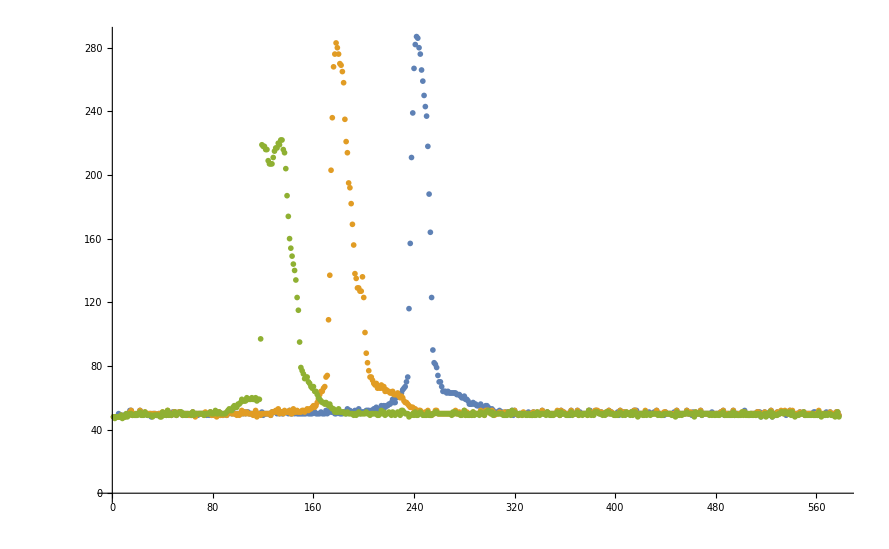

```mathematica
ListPlot[{l,m,r},PlotRange->All,ImageSize->Large]
```

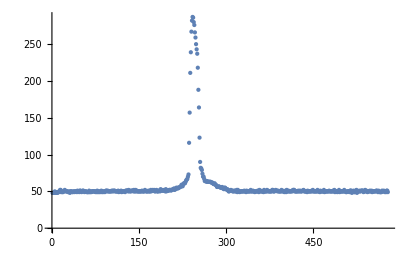
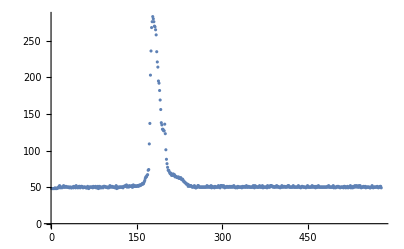
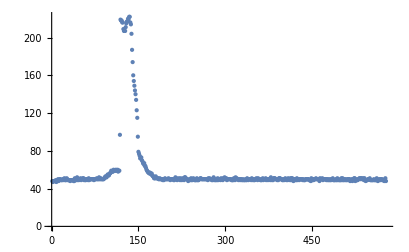

```mathematica
{ListPlot[l,PlotRange->All],ListPlot[m,PlotRange->All],ListPlot[r,PlotRange->All]}
```

```mathematica
x1=230;
y1=260;
Grid[{#[[1]]&/@data[[x1;;y1]],#[[2]]&/@data[[x1;;y1]],#[[3]]&/@data[[x1;;y1]]},Frame->All]
x2=160;
y2=210;
Grid[{#[[1]]&/@data[[x2;;y2]],#[[2]]&/@data[[x2;;y2]],#[[3]]&/@data[[x2;;y2]]},Frame->All]
x3=115;
y3=160;
Grid[{#[[1]]&/@data[[x3;;y3]],#[[2]]&/@data[[x3;;y3]],#[[3]]&/@data[[x3;;y3]]},Frame->All]
```

63 | 65 | 66 | 67 | 70 | 73 | 116 | 157 | 211 | 239 | 267 | 282 | 287 | 286 | 280 | 276 | 266 | 259 | 250 | 243 | 237 | 218 | 188 | 164 | 123 | 90 | 82 | 81 | 79 | 74 | 70
61 | 60 | 58 | 57 | 57 | 56 | 55 | 54 | 54 | 54 | 51 | 53 | 52 | 51 | 52 | 52 | 51 | 50 | 50 | 51 | 50 | 52 | 50 | 49 | 49 | 50 | 50 | 52 | 52 | 50 | 50
52 | 52 | 51 | 50 | 50 | 50 | 48 | 49 | 49 | 50 | 49 | 51 | 49 | 49 | 50 | 51 | 50 | 49 | 49 | 49 | 49 | 51 | 49 | 49 | 49 | 50 | 50 | 51 | 51 | 50 | 50

52 | 51 | 50 | 50 | 50 | 50 | 51 | 50 | 50 | 50 | 52 | 50 | 51 | 52 | 51 | 51 | 52 | 50 | 50 | 51 | 52 | 50 | 50 | 50 | 51 | 51 | 50 | 53 | 51 | 52 | 51 | 51 | 51 | 52 | 51 | 50 | 53 | 50 | 51 | 51 | 51 | 51 | 52 | 52 | 52 | 51 | 52 | 52 | 53 | 53 | 54
55 | 54 | 55 | 57 | 59 | 62 | 64 | 64 | 66 | 67 | 73 | 74 | 109 | 137 | 203 | 236 | 268 | 276 | 283 | 280 | 276 | 270 | 269 | 265 | 258 | 235 | 221 | 214 | 195 | 192 | 182 | 169 | 156 | 138 | 135 | 129 | 129 | 127 | 127 | 136 | 123 | 101 | 88 | 82 | 77 | 73 | 73 | 71 | 69 | 68 | 69
67 | 64 | 64 | 62 | 60 | 59 | 58 | 57 | 57 | 56 | 57 | 56 | 55 | 56 | 54 | 53 | 53 | 51 | 51 | 51 | 53 | 51 | 51 | 51 | 51 | 50 | 50 | 51 | 50 | 50 | 50 | 50 | 49 | 50 | 49 | 50 | 51 | 50 | 50 | 50 | 50 | 50 | 51 | 50 | 50 | 49 | 50 | 50 | 50 | 50 | 50

49 | 50 | 50 | 50 | 51 | 49 | 50 | 50 | 50 | 50 | 50 | 49 | 51 | 51 | 51 | 51 | 50 | 52 | 50 | 51 | 50 | 50 | 51 | 51 | 51 | 50 | 52 | 50 | 50 | 52 | 50 | 51 | 50 | 50 | 50 | 50 | 50 | 50 | 50 | 50 | 51 | 50 | 50 | 50 | 50 | 52
48 | 50 | 50 | 49 | 50 | 50 | 50 | 50 | 50 | 50 | 50 | 49 | 51 | 51 | 51 | 52 | 51 | 53 | 50 | 51 | 51 | 50 | 52 | 51 | 51 | 51 | 52 | 50 | 50 | 53 | 51 | 51 | 52 | 51 | 51 | 51 | 52 | 52 | 51 | 52 | 53 | 52 | 53 | 53 | 54 | 55
58 | 59 | 59 | 97 | 219 | 218 | 218 | 216 | 216 | 209 | 207 | 207 | 207 | 211 | 215 | 217 | 217 | 220 | 219 | 222 | 222 | 216 | 214 | 204 | 187 | 174 | 160 | 154 | 149 | 144 | 140 | 134 | 123 | 115 | 95 | 79 | 77 | 75 | 72 | 73 | 73 | 70 | 69 | 67 | 66 | 67

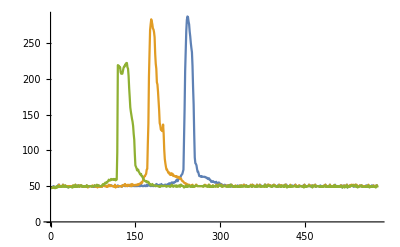

```mathematica
ListLinePlot[{l,m,r},PlotRange->All]
```

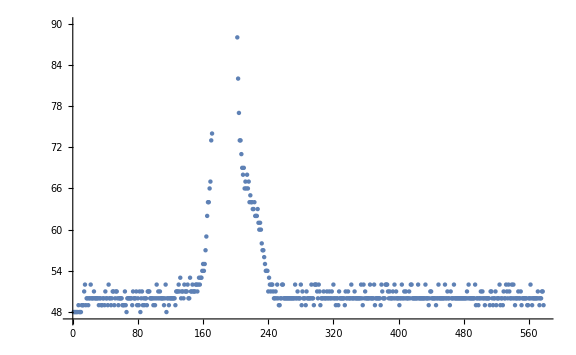

```mathematica
ListPlot[m,PlotRange->{47,90},ImageSize->Large]
```

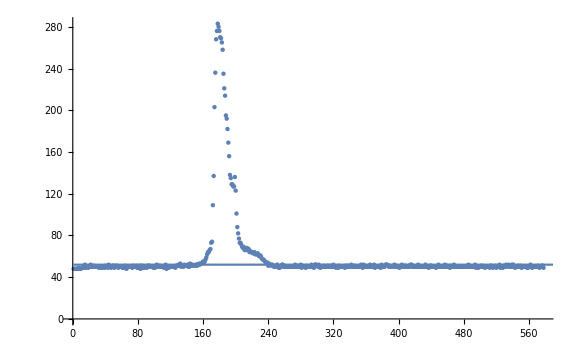

```mathematica
Show[ListPlot[m,PlotRange->All,ImageSize->Large],Plot[{y=52},{x,1,803},ImageSize->Large]]
```

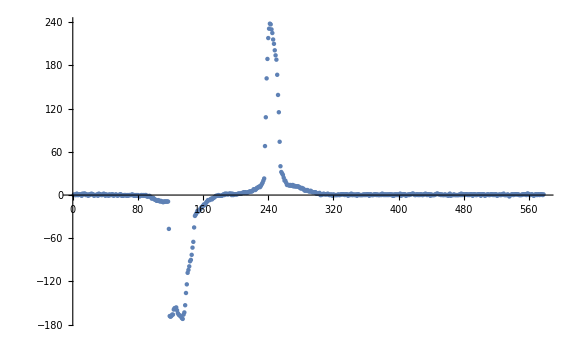

```mathematica
ListPlot[l-r,ImageSize->Large,PlotRange->All]
```

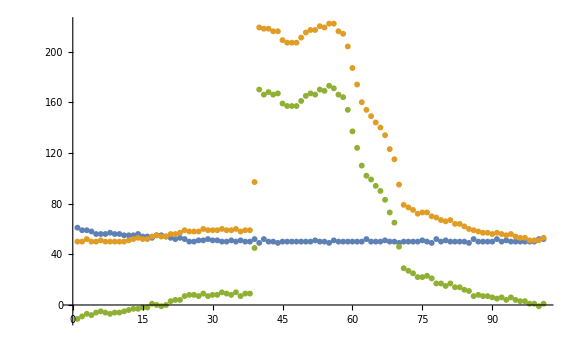

```mathematica
ListPlot[{l[[280;;380]],r[[80;;180]],-l[[280;;380]]+r[[80;;180]]},PlotRange->All,ImageSize->Large]
```

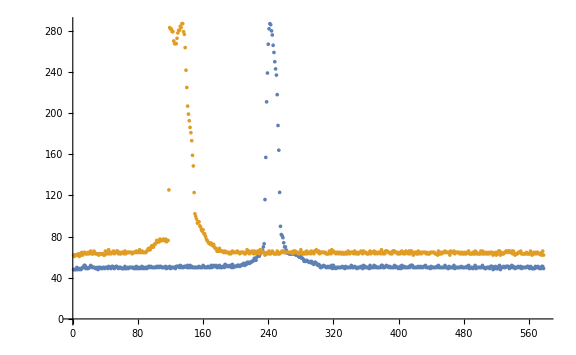
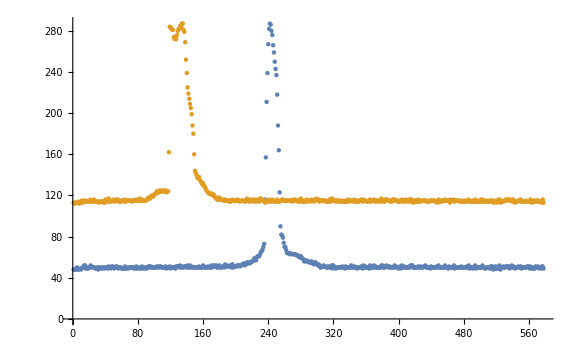

```mathematica
{ListPlot[{l,r*287/222},PlotRange->All,ImageSize->Large],ListPlot[{l,r+287-222},PlotRange->All,ImageSize->Large]}
```

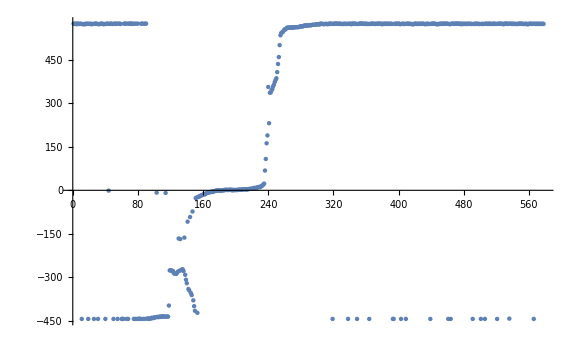

```mathematica
Lm=287;
Lt=52;
Rm=222;
Rt=51;
temp=If[#[[2]]≤ Lt&&#[[1]]≥#[[3]],2Lm-(#[[1]]-#[[3]]),If[#[[2]]≤ Rt&&#[[1]]<#[[3]],-2Rm-(#[[1]]-#[[3]]),#[[1]]-#[[3]]]]&/@data;
ListPlot[temp,PlotRange->All,ImageSize->Large]
```